# RACIONALNA FUNKCIJA

```mathematica
CurrentValue[EvaluationNotebook[],Background]=LightPink
```

RGBColor[1, 0.925, 0.925]

### Lastnosti racionalne funkcije

Racionalna funkcija je okrajšan kvocient dveh polinomov.

```mathematica
f[x_]= p[x]/q[x]
```

p[x]/q[x]

Primer:

p(x) je imenovalec, q(x) pa števec, kjer je p(x) poljuben polinom, q(x) pa poljuben ne ničelni polinom.

Racionalna funkcija je definirana povsod razen v ničlah imenovalca (v polih).

Če je a ničla stopnje k polinoma p(x), pravimo, da je a ničla stopnje k racionalne funkcije f(x).

Če je b ničla stopnje k polinoma q(x), pravimo, da je b pol stopnje k racionalne funkcije f(x).

Racionalna funkcija spremeni predznak le v ničli lihe stopnje in v polu lihe stopnje.

Primer:

```mathematica
h[x_] :=  (x-1)/(x^2 + x -20)
```

```mathematica
p[x_] := x - 1
```

```mathematica
q[x_]:=x^2+x-20
```

### Izračun ničel in polov polinoma

Ničle racionalne funkcije so ničle polinoma v števcu. V zgornjem primeru:

1. način

```mathematica
nicle = x/.N[Solve[p[x] == 0, x]]
```

{1.}

2. način

```mathematica
Solve[Numerator[h[x]==0]]
```

{{x→1}}

Poli racionalne funkcije pa so ničle polinoma v imenovalcu.

```mathematica
poli = x/.N[Solve[q[x] == 0, x]]
```

{-5.,4.}

```mathematica
Solve[Denominator[h[x]] == 0]
```

{{x→-5},{x→4}}

### Vedenje racionalne funkcije v neskončnosti

Ločimo 3 primere:

Če je stopnja števca manjša od stopnje imenovalca se daleč proč od izhodišča graf približuje abcisni osi, ki je vodoravna asimptota grafa.

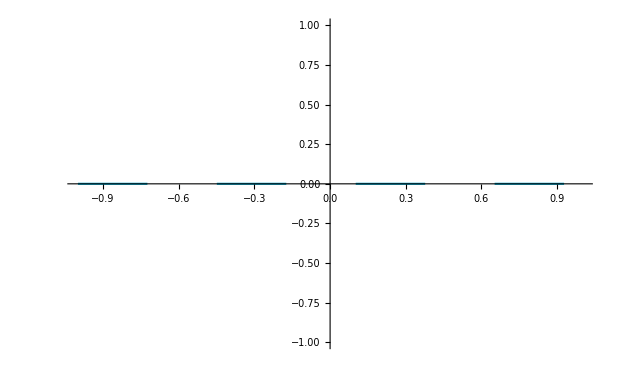

```mathematica
Plot[0,{x, -1,1}, PlotStyle->Dashing[{0.1,0.1}]]
```

Če je stopnja števca enaka stopnji imenovalca je vodoravna asimptota grafa premica količnik vodilnih členov.

```mathematica
s[x_]:= (2x^2 +4x)/(4x^2-2x)
```

V tem primeru je vodoravna asimptota enaka y = 1/2

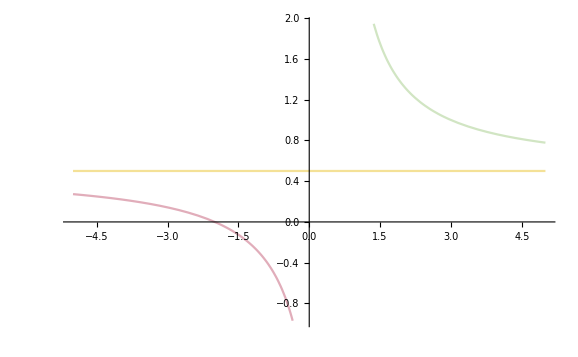

```mathematica
Plot[{s[x],0.5},{x,-5,5},ColorFunction->ColorData["Pastel"]]
```

Če pa je stopnja števca večja od stopnje imenovalca, potem se daleč stran od izhodišča graf racionalne funkcije približuje grafu polinoma, ki ga dobimo kot količnik pri deljenju polinoma v števcu s polinomom v imenovalcu.

Če je k(x) linearen polinom potem ima graf poševno asimptoto. V nasprotnem primeru ima graf asimptotično krivuljo.

Vodoravno simptoto, poševno asimptoto ali asimptotično krivuljo lahko graf seka ali ne. Asimptota v ničlah ostanka graf seke ali pa se ga dotika.

### Graf racionalne funkcije

Nekaj primerov grafov:

1. primer

```mathematica
g[x_] := 1 / (x^2-9)
```

Ničle:

```mathematica
Solve[Numerator [g[x]]== 0]
```

{}

Poli:

```mathematica
Solve[Denominator[g[x]]==0]
```

{{x→-3},{x→3}}

Obnašanaje v neskončnosti:

-vodilni člen je v imenovalcu manjši kot v števcu, zato je asimptota y = 0.

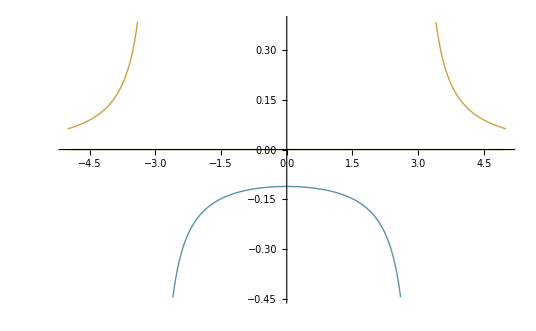

```mathematica
Plot[{g[x], 0}, {x, -5,5}, ColorFunction->"Rainbow", PlotStyle->Thick]
```

2.primer

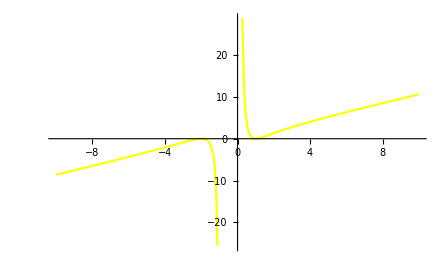

```mathematica
Plot[(x^4+2 x^3-3 x^2-4x+4)/(x^3+x^2), {x, -10,10}, PlotStyle->{Yellow}]
```

3. primer

```mathematica
t[x_]:= (-x^3-2 x^2-x)/(x+2)
```

```mathematica
c[x_]:=(x^3+4 x^2-3x-18)/(x^2-4x-5)
```

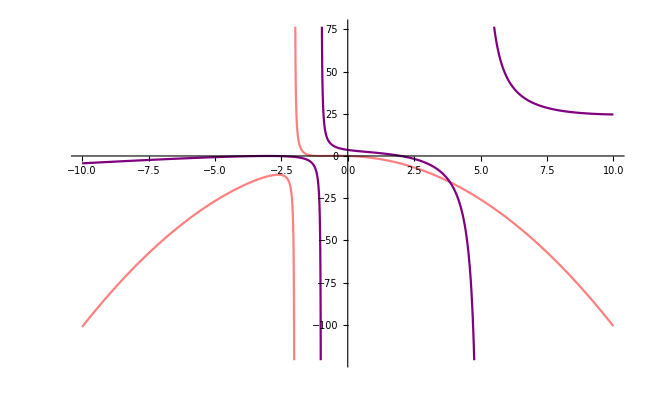

```mathematica
Plot[{t[x],c[x]},{x,-10,10}, PlotStyle->{Pink, Purple}]
```

4.primer

```mathematica
ClearAll
```

ClearAll

```mathematica
f[x_,a_]:= (x^(a+1)-2 x^a+6)/(x^2-x+6)
```

```mathematica
Manipulate[Plot[ f[x,a], {x,-10,10},PlotStyle->Thick, PlotRange->Automatic],{a,0,10}]
```